```mathematica
T={{1,-1/2},{-1/2,1}}//N
```

{{1.,-0.5},{-0.5,1.}}

```mathematica
{ev,P}=Eigensystem[T]
```

{{1.5,0.5},{{-0.707107,0.707107},{-0.707107,-0.707107}}}

```mathematica
P.T.Transpose[P]
```

{{1.5,0.},{0.,0.5}}

```mathematica
ArcTan[P[[1,1]],P[[1,2]] ]
```

2.35619

```mathematica
plotEllipse[a_,b_,c_]:=ContourPlot[-a x^2 -b y^2 -2 c x y,{x, -2,2},{y,-2,2}]
```

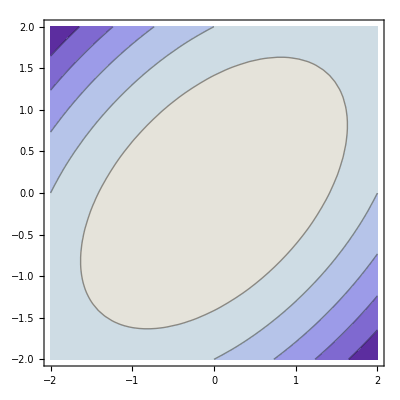

```mathematica
plotEllipse[1,1,-1/2]
```

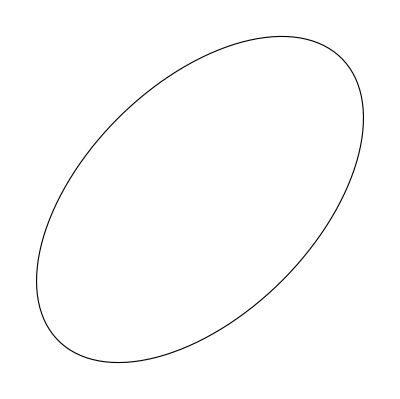

```mathematica
ellipse[{0,0},1,1,-1/2,1]//Graphics
```